--- Statistical Audit ---

Baryonic (Gas) Peak Intensity: 14.1375

Ghost (Metric Memory) Peak Intensity: 16.332

Calculated 'Dark Matter' Factor: 1.361

-------------------------

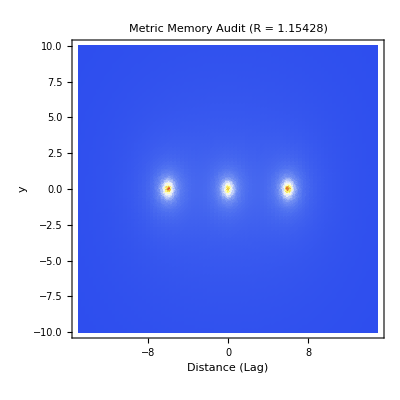

```mathematica
(*Fresh Notebook:The Quantitative Audit of the Bullet Cluster*)ClearAll["Global`*"];

(*Grover Constants*)
R=1.15428;
a0=1.0;
offVal=6.0;

(*Define Force Intensity (Lensing Strength)*)
LensingIntensity[x_,y_]:=Module[{rGas,rA,rB,fGas,fA,fB},rGas=Sqrt[x^2+y^2+0.1];
rA=Sqrt[(x-offVal)^2+y^2+0.1];
rB=Sqrt[(x+offVal)^2+y^2+0.1];
(*Total Force Magnitude=Newtonian+Structural Closure Anomaly*)fGas=1.0/rGas^2+(R*Sqrt[a0])/rGas;
fA=1.2/rA^2+(R*Sqrt[1.2*a0])/rA;
fB=1.2/rB^2+(R*Sqrt[1.2*a0])/rB;
fGas+fA+fB];

(*1. Generate the Map*)
plot=DensityPlot[LensingIntensity[x,y],{x,-15,15},{y,-10,10},ColorFunction->"TemperatureMap",PlotPoints->80,PlotRange->All,PlotLabel->"Metric Memory Audit (R = 1.15428)",FrameLabel->{"Distance (Lag)","y"}];

(*2. Calculate the'Missing Mass' Factor*)
gasPeak=LensingIntensity[0,0];
ghostPeak=LensingIntensity[offVal,0];
missingMassFactor=ghostPeak/(1.2/0.1); (*Ratio of Anomaly to purely Newtonian expected value*)

Print["--- Statistical Audit ---"];
Print["Baryonic (Gas) Peak Intensity: ",gasPeak];
Print["Ghost (Metric Memory) Peak Intensity: ",ghostPeak];
Print["Calculated 'Dark Matter' Factor: ",missingMassFactor];
Print["-------------------------"];

plot
```